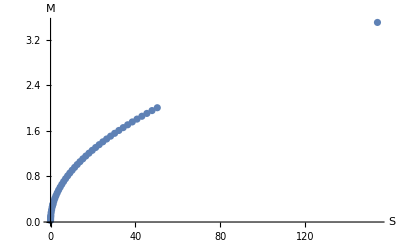

```mathematica
MS1=Table[{Con1[[i]][[1]]^2 Pi,Con1[[i,3]]}, {i,total1-3}];
MS1plot=ListPlot[MS1,AxesLabel->{Style[" S",FontSize->18],Style["M", FontSize->18]},PlotRange->All]
```

```mathematica
MS2=Table[{Con2[[i]][[1]]^2 Pi,Con2[[i,3]]}, {i,total2}];
```

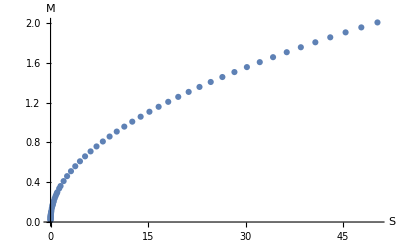

```mathematica
MS2plot=ListPlot[MS2,AxesLabel->{Style[" S",FontSize->18],Style["M", FontSize->18]},PlotRange->All]
```

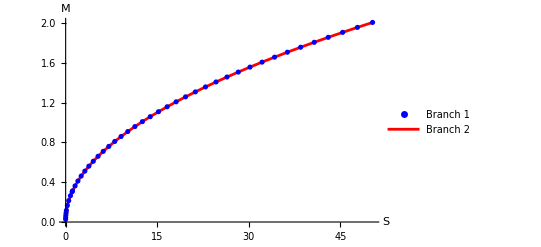

```mathematica
ListPlot[{MS1,MS2},PlotStyle->{Blue,Red},Joined->{False, True},AxesLabel->{Style["S",FontSize->20],Style["M",FontSize->20]},PlotLegends->Placed[{Style["Branch 1",FontSize->18],Style["Branch 2",FontSize->18]},{0.2,0.9}],PlotRange->All,ImageSize->400]
```